```mathematica
Table[allGraphs[k,"comp"]=Equal;allGraphs[k,"compwhy"]="In terminis",{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{In terminis,In terminis,In terminis,In terminis,In terminis}

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

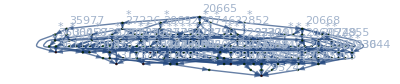

```mathematica
Graph[DependencyGraph[allGraphs,lambdaKey],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top}]
```

```mathematica
Select[Keys[allGraphs],allGraphs[#,"comp"]==Equal&]
```

{29524,29560,29608,29633,29797,30334,31714,31738,31954,31492,31444,36086,36112,36138,36166,36030,36817,35406,35434,38281,33916,33834,22318,25168,24922,49210,51475,11950,11680,7738,448}

```mathematica
doubters=Select[Keys[allGraphs],allGraphs[#,"comp"]==GreaterEqual&&With[{g=allGraphs[#,"graph"]},VertexCount[g]==3]&]
```

{}

```mathematica
Table[Labeled[allGraphs[k,"graph"],Style[k,ColourForKey[allGraphs,k]]],{k,doubters}]
```

{}

```mathematica
allGraphs[22318,"children"]
```

{{29608,36898},{29608,36898}}

```mathematica
allGraphs[22318,"parents"]
```

{22312,22284,22156,22146,22060,22038,22038,22038,22038,21886,19969,19959,19699,2473,2463,2203,448,448}

```mathematica
DependencyGraph5[assoc_,startKey_]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={}},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
visited=Append[visited,currentKey];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
vertexColors=Append[vertexColors,currentKey->ColourForKey[assoc,currentKey]];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
Tooltip[
currentKey,
Labeled[
Column[
{
Style[currentKey,Bold],
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,size}],Table[Style[k,Red],{k,size}]}]
,
Row[{
assoc[currentKey]["graph"],
Graph[
VertexList[assoc[currentKey]["graph"]],
EdgeList[assoc[currentKey]["graph"]],
VertexLabels->PropertyValue[assoc[currentKey]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[assoc[currentKey]["children"],Italic],
Style[assoc[currentKey]["colofour"]/.repcolofour5textBase,Italic]
},
Center
],Style[assoc[currentKey]["compwhy"],Bold]]]];
children=assoc[currentKey,"children"];
Table[
Table[
If[True(*!MemberQ[visited,child]*),
vertexLabels=Append[vertexLabels,childCouple->Tooltip["*",
Column[{
Style[currentKey,Bold,ColourForKey[assoc,currentKey]]
,
Row[{
Style[childCouple[[1]],ColourForKey[assoc,childCouple[[1]]]],
"   ",
Style[childCouple[[2]],ColourForKey[assoc,childCouple[[2]]]]
}
]}]]];
vertexColors=Append[vertexColors,childCouple->ColourForRelation[assoc,currentKey,childCouple]];
edges=Append[edges,childCouple->child];
edges=Append[edges,currentKey->childCouple];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
],
{Length[todo],Length[visited]}
];
Graph[
vertices,
DeleteDuplicates[edges],
VertexStyle->DeleteDuplicates[vertexColors], 
VertexLabels->DeleteDuplicates[vertexLabels],
GraphLayout->"RadialEmbedding",
EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->.001}]
]
]
```

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,baseKeys5}]
```

{v12345→v12345,v1234x5→v1234x5,v1235x4→v1235x4,v123x45→v123x45,v123x4x5→v123x4x5,v1245x3→v1245x3,v124x35→v124x35,v124x3x5→v124x3x5,v125x34→v125x34,v125x3x4→v125x3x4,v12x345→v12x345,v12x34x5→v12x34x5,v12x35x4→v12x35x4,v12x3x45→v12x3x45,v12x3x4x5→v12x3x4x5,v1345x2→v1345x2,v134x25→v134x25,v134x2x5→v134x2x5,v135x24→v135x24,v135x2x4→v135x2x4,v13x245→v13x245,v13x24x5→v13x24x5,v13x25x4→v13x25x4,v13x2x45→v13x2x45,v13x2x4x5→v13x2x4x5,v145x23→v145x23,v145x2x3→v145x2x3,v14x235→v14x235,v14x23x5→v14x23x5,v14x25x3→v14x25x3,v14x2x35→v14x2x35,v14x2x3x5→v14x2x3x5,v15x234→v15x234,v15x23x4→v15x23x4,v15x24x3→v15x24x3,v15x2x34→v15x2x34,v15x2x3x4→v15x2x3x4,v1x2345→v1x2345,v1x234x5→v1x234x5,v1x235x4→v1x235x4,v1x23x45→v1x23x45,v1x23x4x5→v1x23x4x5,v1x245x3→v1x245x3,v1x24x35→v1x24x35,v1x24x3x5→v1x24x3x5,v1x25x34→v1x25x34,v1x25x3x4→v1x25x3x4,v1x2x345→v1x2x345,v1x2x34x5→v1x2x34x5,v1x2x35x4→v1x2x35x4,v1x2x3x45→v1x2x3x45,v1x2x3x4x5→v1x2x3x4x5}

```mathematica
Table[Labeled[Graph[DependencyGraph5[allGraphs,allGraphs[k,"parents"]//First],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top}],k],{k,doubters}]
```

{}

```mathematica
Table[allGraphs[k,"comp"]=Equal;allGraphs[k,"compwhy"]="In terminis",{k,doubters}]
```

{}

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,baseKeys5}]
```

{v12345→v12345,v1234x5→v1234x5,v1235x4→v1235x4,v123x45→v123x45,v123x4x5→v123x4x5,v1245x3→v1245x3,v124x35→v124x35,v124x3x5→v124x3x5,v125x34→v125x34,v125x3x4→v125x3x4,v12x345→v12x345,v12x34x5→v12x34x5,v12x35x4→v12x35x4,v12x3x45→v12x3x45,v12x3x4x5→v12x3x4x5,v1345x2→v1345x2,v134x25→v134x25,v134x2x5→v134x2x5,v135x24→v135x24,v135x2x4→v135x2x4,v13x245→v13x245,v13x24x5→v13x24x5,v13x25x4→v13x25x4,v13x2x45→v13x2x45,v13x2x4x5→v13x2x4x5,v145x23→v145x23,v145x2x3→v145x2x3,v14x235→v14x235,v14x23x5→v14x23x5,v14x25x3→v14x25x3,v14x2x35→v14x2x35,v14x2x3x5→v14x2x3x5,v15x234→v15x234,v15x23x4→v15x23x4,v15x24x3→v15x24x3,v15x2x34→v15x2x34,v15x2x3x4→v15x2x3x4,v1x2345→v1x2345,v1x234x5→v1x234x5,v1x235x4→v1x235x4,v1x23x45→v1x23x45,v1x23x4x5→v1x23x4x5,v1x245x3→v1x245x3,v1x24x35→v1x24x35,v1x24x3x5→v1x24x3x5,v1x25x34→v1x25x34,v1x25x3x4→v1x25x3x4,v1x2x345→v1x2x345,v1x2x34x5→v1x2x34x5,v1x2x35x4→v1x2x35x4,v1x2x3x45→v1x2x3x45,v1x2x3x4x5→v1x2x3x4x5}

```mathematica
Table[Labeled[Graph[DependencyGraph5[allGraphs,allGraphs[k,"parents"]//First],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top}],k],{k,doubters}]
```

{}

```mathematica
doubters2=Select[Keys[allGraphs],allGraphs[#,"comp"]==Equal&]//Length
```

31

```mathematica
hoekcontracted=Select[Keys[allGraphs],allGraphs[#,"vertexsets"]=={{1},{2,5},{3},{4}}&&EdgeCount[allGraphs[#,"graph"]]==4&]
```

{29460,29296,29223,27355,27282,27118,22981,22908,22744,20803,9130,9057,8893,6952,2578}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,hoekcontracted}]
```

{-Graphics-29460,-Graphics-29296,-Graphics-29223,-Graphics-27355,-Graphics-27282,-Graphics-27118,-Graphics-22981,-Graphics-22908,-Graphics-22744,-Graphics-20803,-Graphics-9130,-Graphics-9057,-Graphics-8893,-Graphics-6952,-Graphics-2578}

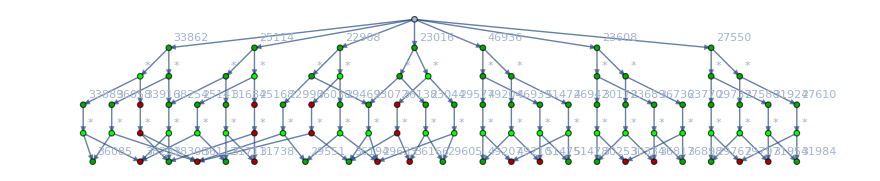

```mathematica
Graph[DependencyGraph[allGraphs,{33862,46936,25114,23608,
27550,23016,22908}],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top}]
```